```mathematica
(*Import packages*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

CT::shdw: Symbol CT appears in multiple contexts {CalcTools`,Global`}; definitions in context CalcTools` may shadow or be shadowed by other definitions.

## Square amplitudes

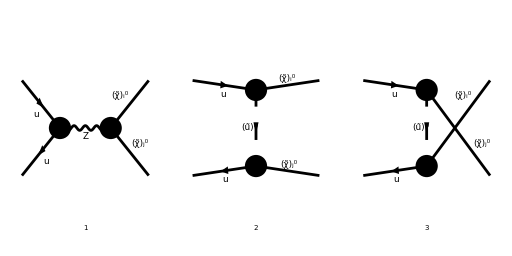

```mathematica
treeDiagrams = InsertFields[
CreateTopologies[0, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], 
{F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD,
Restrictions->{NoLightFHCoupling,NoElectronHCoupling},
ExcludeParticles->{F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, 0][0]=FCFAConvert[
CreateFeynAmp[treeDiagrams], 
IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules/.{IndexDelta->FeynCalc`IndexDelta};
```

```mathematica
temp=SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
```

```mathematica
Subscript[M, 0][1]=temp*DiracSimplify/@(Subscript[M, 0][0]/temp/.ZSimplifyRules/.QSimplifyRules);
Subscript[M, 0][2]=Subscript[M, 0][1]/.{Conjugate[Opp[i_,j_,L]]->-Opp[i,j,R]}//.SuperChargeRules;
```

```mathematica
MakeBoxes[DSf[s_,t_,g_],TraditionalForm]:=SubscriptBox["Δ",MakeBoxes[s,TraditionalForm]]
MakeBoxes[DSfC[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"*"]
MakeBoxes[DZ,TraditionalForm]=SubscriptBox["Δ","Z"]
MakeBoxes[FeynCalc`Index[Sfermion,a_],TraditionalForm]:=MakeBoxes[a,TraditionalForm]

MakeBoxes[Den[p2_,m2_],TraditionalForm]:=MakeBoxes[1/(p2-m2),TraditionalForm]
MakeBoxes[tMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"t"]
MakeBoxes[uMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"u"]
```

SubscriptBox[Δ,Z]

```mathematica
Subscript[M, s][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],1]]/.SMP["m_Z"]^2->DZ;
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],2]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],3]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
```

```mathematica
Subscript[M̄, s][0]=ConjugateAmplitude[Subscript[M, s][0]];
Subscript[M̄, t][0]=ConjugateAmplitude[Subscript[M, t][0]];
Subscript[M̄, u][0]=ConjugateAmplitude[Subscript[M, u][0]];
```

```mathematica
(*Common prefactor for the squared amplitudes.*)
Prefactor=4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
```

```mathematica
(*Square the amplitudes*)
Subscript[I, ss][0]=SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, s][0]];
Subscript[I, tt][0]=SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, t][0]/.A->B];
Subscript[I, uu][0]=SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, u][0]/.A->B];
Subscript[I, st][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, t][0]]+SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, s][0]])/2;
Subscript[I, su][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, u][0]]+SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, s][0]])/2;
Subscript[I, tu][0]=(SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, u][0]/.A->B]+SquareAmplitudes[Subscript[M, u][0]/.A->B,Subscript[M̄, t][0]])/2;
```

```mathematica
(*Function for taking the limit D->4 of an expression.*)
FixDimension[amp_]:=(SelectFree2[#1,Eps]&)[
ChangeDimension[amp,4]/.{D->4}//FeynAmpDenominatorExplicit//DiracSimplify//Simplify
];
```

```mathematica
(*Function for collecting the available kinemtic terms.*)
IsolateKinematicTerms={
(t-MNeu[i])(t-MNeu[j])->KT[1],
(u-MNeu[i])(u-MNeu[j])->KT[2],
MNeu[i]MNeu[j]s->KT[3]};
KinematicTerms={KT[1],KT[2],KT[3]};
FreeKinematicTerms={
KT[1]->(t-MNeu[i])(t-MNeu[j]),
KT[2]->(u-MNeu[i])(u-MNeu[j]),
KT[3]->MNeu[i]MNeu[j]s};
CollectTerms[amp_]:=Collect2[ReduceMandelstam[amp]/.IsolateKinematicTerms,KinematicTerms]/.FreeKinematicTerms
```

```mathematica
(*Function for converting propagator denominators to a Den-function with Breit-Wigner mass replacements.*)
Convert2Den={
t-DSf[args__]->1/Den[t,DSf[args]],
u-DSf[args__]->1/Den[u,DSf[args]],
t-DSfC[args__]->1/Den[t,DSfC[args]],
u-DSfC[args__]->1/Den[u,DSfC[args]],
s-DZ->1/Den[s,DZ],
s-DZ*->1/Den[s,DZ*],
DZ-s->-1/Den[s,DZ],
DZ*-s->-1/Den[s,DZ*]
};
DenominatorFactors={
Den[t,m1_]Den[u,m2_],
Den[s,m1_]Den[u,m2_],
Den[s,m1_]Den[t,m2_]
};
FactorDenominators[expr_]:=Prefactor Collect[
FixDimension[(expr/Prefactor)/.Convert2Den]//Expand,
DenominatorFactors,
CollectTerms
]
```

```mathematica
(*Substitute the propagator factors.*)
Subscript[I, ss][1]=FactorDenominators[Subscript[I, ss][0]]
Subscript[I, tt][1]=FactorDenominators[Subscript[I, tt][0]]
Subscript[I, uu][1]=FactorDenominators[Subscript[I, uu][0]]
Subscript[I, st][1]=FactorDenominators[Subscript[I, st][0]]
Subscript[I, su][1]=FactorDenominators[Subscript[I, su][0]]
Subscript[I, tu][1]=FactorDenominators[Subscript[I, tu][0]]
```

4 g_W^4 δ_ab^2 (1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Z_s^L Conjugate[(Z_s^L)]+Z_s^R Conjugate[(Z_s^R)]) (2 m_i^2 m_j^2-t m_i^2-u m_i^2-t m_j^2-u m_j^2+t^2+u^2)-s m_i m_j 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))

4 g_W^4 δ_ab^2 (t-m_i^2) (t-m_j^2) 1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) (Q_SfeA^(L L̄) Conjugate[(Q_SfeB^(L L̄))]+Q_SfeB^(R R̄) Conjugate[(Q_SfeA^(R R̄))]+Q_SfeA^LR Conjugate[(Q_SfeB^LR)]+Q_SfeB^RL Conjugate[(Q_SfeA^RL)])

4 g_W^4 δ_ab^2 (u-m_i^2) (u-m_j^2) 1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) (Q_SfeB^(L L̄) Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^RL Conjugate[(Q_SfeB^RL)]+Q_SfeB^LR Conjugate[(Q_SfeA^LR)])

4 g_W^4 δ_ab^2 (1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (1/2 (t-m_i^2) (t-m_j^2) (Z_s^R Conjugate[(Q_SfeA^(R R̄))]+Z_s^L Q_SfeA^(L L̄))-1/2 s m_i m_j (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))]))+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (1/2 (t-m_i^2) (t-m_j^2) (Conjugate[(Z_s^L)] Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])-1/2 s m_i m_j (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Q_SfeA^(R R̄))))

4 g_W^4 δ_ab^2 (1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (1/2 (u-m_i^2) (u-m_j^2) (Z_s^R Conjugate[(Q_SfeA^(R R̄))]+Z_s^L Q_SfeA^(L L̄))-1/2 s m_i m_j (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))]))+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (1/2 (u-m_i^2) (u-m_j^2) (Conjugate[(Z_s^L)] Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])-1/2 s m_i m_j (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Q_SfeA^(R R̄))))

4 g_W^4 δ_ab^2 (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (1/2 (t u-m_i^2 m_j^2) (Q_SfeA^LR Conjugate[(Q_SfeB^RL)]+Q_SfeB^LR Conjugate[(Q_SfeA^RL)])-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))+1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB) (1/2 (t u-m_i^2 m_j^2) (Q_SfeA^RL Conjugate[(Q_SfeB^LR)]+Q_SfeB^RL Conjugate[(Q_SfeA^LR)])-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄))))

```mathematica
(*Temporary variables for the expanded kinematic terms.*)
tij=((t-MNeu[i]^2)(t-MNeu[j]^2))//Expand;
uij=((u-MNeu[i]^2)(u-MNeu[j]^2))//Expand;
```

```mathematica
(*Add squared amplitudes together, omitting prefactor and prettifying kinematic terms.*)
Itot[0]=(Subscript[I, ss][1]+Subscript[I, tt][1]+Subscript[I, uu][1]+2 Subscript[I, st][1]+2 Subscript[I, su][1]+2 Subscript[I, tu][1])/Prefactor;
Itot[1]=Itot[0]/.{tij+uij->(t-MNeu[i]^2)(t-MNeu[j]^2)+(u-MNeu[i]^2)(u-MNeu[j]^2)}
```

1/(4 δ_ab^2 g_W^4)(4 1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) δ_ab^2 (u-m_i^2) (u-m_j^2) (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) g_W^4+4 1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) δ_ab^2 (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) g_W^4+8 δ_ab^2 (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (1/2 (t u-m_i^2 m_j^2) (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))+1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB) (1/2 (t u-m_i^2 m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))) g_W^4+4 δ_ab^2 (1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((t-m_i^2) (t-m_j^2)+(u-m_i^2) (u-m_j^2)) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R)-s 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) m_i m_j ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2)) g_W^4+8 δ_ab^2 (1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (1/2 (t-m_i^2) (t-m_j^2) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (1/2 (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))) g_W^4+8 δ_ab^2 (1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (1/2 (u-m_i^2) (u-m_j^2) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (1/2 (u-m_i^2) (u-m_j^2) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))) g_W^4)

```mathematica
(*Show that the total amplitude can be written as effective charges in front of these four kinematic terms.*)
Collect[
Itot[1],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(2000) s m_i m_j+Q(2008) (t u-m_i^2 m_j^2)+Q(2005) (t-m_i^2) (t-m_j^2)+Q(2007) (u-m_i^2) (u-m_j^2)

## Integrate over t

```mathematica
(*To simplify before integrating over t, we will need to convert all terms containing u to t.*)
Itot[2]=Collect[
Itot[1]/.{Den[u,DSf[args__]]->-Den[t,uMass[args]],Den[u,DSfC[args__]]->-Den[t,uMass[args]*],Den[t,DSf[args__]]->Den[t,tMass[args]],Den[t,DSfC[args__]]->Den[t,tMass[args]*]}/.{u->MNeu[i]^2+MNeu[j]^2-s-t}//Expand,
Den[args1__]Den[args2__],
Simplify
]
```

1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^u) (-m_i^2+s+t) (-m_j^2+s+t) (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))+1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^t) (Conjugate[(Q_SfeA^RL)] Q_SfeB^LR t^2-Conjugate[(Q_SfeA^RL)] m_i^2 Q_SfeB^LR t-Conjugate[(Q_SfeA^RL)] m_j^2 Q_SfeB^LR t+s Conjugate[(Q_SfeA^RL)] Q_SfeB^LR t+s Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))] m_i m_j+Conjugate[(Q_SfeB^RL)] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)) Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] m_i^2 m_j^2 Q_SfeB^LR+s m_i m_j Q_SfeA^(L L̄) Q_SfeB^(L L̄))+1/(t-Conjugate[(Δ_SfeB^t)]) 1/(t-Δ_SfeA^t) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))+1/(t-Conjugate[(Δ_SfeA^t)]) 1/(t-Δ_SfeB^u) (Conjugate[(Q_SfeA^LR)] Q_SfeB^RL t^2-Conjugate[(Q_SfeA^LR)] m_i^2 Q_SfeB^RL t-Conjugate[(Q_SfeA^LR)] m_j^2 Q_SfeB^RL t+s Conjugate[(Q_SfeA^LR)] Q_SfeB^RL t+s Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))] m_i m_j+Conjugate[(Q_SfeB^LR)] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)) Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] m_i^2 m_j^2 Q_SfeB^RL+s m_i m_j Q_SfeA^(R R̄) Q_SfeB^(R R̄))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_SfeA^t)]) (Conjugate[(Q_SfeA^(L L̄))] (Conjugate[(Z_s^L)] (t-m_i^2) (t-m_j^2)-s m_i m_j Z_s^L)+Q_SfeA^(R R̄) (Conjugate[(Z_s^R)] (t-m_i^2) (t-m_j^2)-s m_i m_j Z_s^R))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA^u) (Conjugate[(Q_SfeA^(L L̄))] (s m_i m_j Z_s^L-Conjugate[(Z_s^L)] (-m_i^2+s+t) (-m_j^2+s+t))+Q_SfeA^(R R̄) (s m_i m_j Z_s^R-Conjugate[(Z_s^R)] (-m_i^2+s+t) (-m_j^2+s+t)))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA^t) (-Q_SfeA^(L L̄) (s Conjugate[(Z_s^L)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^L)-Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^R))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_SfeA^u)]) (Q_SfeA^(L L̄) (s Conjugate[(Z_s^L)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^L)+Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^R))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-s m_i m_j (Conjugate[(Z_s^L)])^2+(s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))

```mathematica
(*Convert all t-dependence to a dictionary of standard t-integrals Subscript[T, d]^p(Subscript[Δ, 1],...,Subscript[Δ, d]).*)
ItotIntegrals[0]=ToTIntegrals[Itot[2]]
ItotIntegrals[1]=ReduceTIntegrals[ToTIntegrals[Itot[2]]]
```

CT(2042) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])-CT(2050) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(2041) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(2040) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2044) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2049) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2052) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2048) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2051) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2046) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2053) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2045) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2018) T_1^0(Conjugate[(Δ_SfeA^t)])-CT(2034) T_1^1(Conjugate[(Δ_SfeA^t)])+CT(2037) T_1^2(Conjugate[(Δ_SfeA^t)])+CT(2023) T_1^0(Conjugate[(Δ_SfeA^u)])-CT(2058) T_1^1(Conjugate[(Δ_SfeA^u)])-CT(2060) T_1^2(Conjugate[(Δ_SfeA^u)])+CT(2027) T_1^0(Δ_SfeA^t)-CT(2059) T_1^1(Δ_SfeA^t)+CT(2061) T_1^2(Δ_SfeA^t)+CT(2031) T_1^0(Δ_SfeA^u)-CT(2036) T_1^1(Δ_SfeA^u)-CT(2038) T_1^2(Δ_SfeA^u)+CT(2014) T_0^0+2 CT(2055) T_0^1+2 CT(2056) T_0^2

CT(2073) T_1^0(Conjugate[(Δ_SfeA^t)])+CT(2081) T_1^0(Conjugate[(Δ_SfeA^u)])+CT(2087) T_1^0(Δ_SfeA^t)+CT(2089) T_1^0(Δ_SfeA^u)+CT(2075) T_1^0(Conjugate[(Δ_SfeB^t)])+CT(2084) T_1^0(Conjugate[(Δ_SfeB^u)])+CT(2066) T_0^0+CT(2069) T_0^1+2 CT(2056) T_0^2

```mathematica
(*We can write it out in terms of the basic charges using GetKinematicCoefficients.*)
Collect[ItotIntegrals[0],tIntegral[args__],GetKinematicCoefficients]
```

m_i^2 (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)]) m_j^2+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_i^2+(-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_j^2+s (2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2)) T_0^1+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^2+1/(s-Δ_Z) ((-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Conjugate[(Δ_SfeA^t)])+1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+s (-2 Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-2 Conjugate[(Z_s^R)] Q_SfeA^(R R̄))+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Δ_SfeA^u)+1/(s-Δ_Z) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Conjugate[(Δ_SfeA^t)])+1/(s-Conjugate[(Δ_Z)]) (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Δ_SfeA^u)+(m_i^2 (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) m_j^2+s m_i (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)) m_j) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+(m_i^2 (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) m_j^2+s m_i (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)) m_j) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s^2+m_i^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s+m_i^2 m_j^2 (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+((-Conjugate[(Q_SfeB^LR)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^LR)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)+s (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+((-Conjugate[(Q_SfeB^LR)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^RL-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^LR)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^RL-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeB^RL)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)+s (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))+s (2 Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+2 Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+2 Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+2 Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+(Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+(Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+1/(s-Δ_Z) T_1^2(Conjugate[(Δ_SfeA^u)]) (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^2(Δ_SfeA^t) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^1(Δ_SfeA^t) ((-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+m_j^2 (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^1(Conjugate[(Δ_SfeA^u)]) ((Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+s (-2 Q_SfeA^(L L̄) Z_s^L-2 Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+m_j^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_SfeA^u)]) ((-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s^2+m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)) s+m_i^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_j^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_i^2 m_j^2 (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_SfeA^t) (m_i^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_j^2+s m_i (-Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)) m_j)+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_SfeA^t)]) (m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_j^2+s m_i (-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Q_SfeA^(R R̄) Z_s^R) m_j)+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_SfeA^u) ((-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s^2+m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^0 ((Abs[Z_s^L]^2+Abs[Z_s^R]^2) s^2+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_i^2 s+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_j^2 s+m_i m_j (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2) s+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) m_i^2 m_j^2)

```mathematica
(*A function for collecting all effective charges in an expression.*)
EffectiveCharges={
Qtu[args1__]Qtu[args2__],
Qtu[args1__]Qtu[args2__]*,
Qtu[args1__]*Qtu[args2__]*,
QtuC[args1__]QtuC[args2__],
QtuC[args1__]QtuC[args2__]*,
QtuC[args1__]*QtuC[args2__]*,
Zs[arg_]QtuC[args__],
Zs[arg_]*QtuC[args__],
Zs[arg_]QtuC[args__]*,
Zs[arg_]*QtuC[args__]*
};
CollectEffCharges[expr_]:=Collect2[
Collect[
FRH[expr]//Expand,
EffectiveCharges,
(Isolate[#1//Simplify]&)
],
KK[arg_]
]
```

```mathematica
(*Write out the analytic results of all the Subscript[T, d]^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.*)
ItotIntegrals[2]=Collect[
FreeTIntegrals[ItotIntegrals[0]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2123) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2128) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2144) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2151) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+KK(2155) log((t1-Conjugate[(Δ_SfeB^t)])/(t0-Conjugate[(Δ_SfeB^t)]))+KK(2161) log((t1-Conjugate[(Δ_SfeB^u)])/(t0-Conjugate[(Δ_SfeB^u)]))+KK(2166) log((t1-Δ_SfeB^u)/(t0-Δ_SfeB^u))+2/3 KK(2111) (t1^3-t0^3)+KK(2110) (t1^2-t0^2)+KK(2104) (t1-t0)

```mathematica
(*Collect terms that can combine under A<->B.*)
BindexLogs={
Log[(t1-tMass[Index[Sfermion,B],args__]*)/(t0-tMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__]*)/(t0-uMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__])/(t0-uMass[Index[Sfermion,B],args__])]
};
ItotIntegrals[3]=Collect[
((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2169) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2176) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2144) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2182) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+2/3 KK(2111) (t1^3-t0^3)+KK(2110) (t1^2-t0^2)+KK(2104) (t1-t0)

```mathematica
(*Conjugate total expression to assert if result is real.*)
ItotIntegralsC[0]=Refine[
Collect[
ItotIntegrals[3],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
]/.{Log[arg_]->Log[arg*]}/.{Den[p_,m_]*->Den[p*,m*]},
Assumptions->{t1∈Reals,t0∈Reals,MNeu[i_]∈PositiveReals,s∈PositiveReals}
];
ItotIntegralsC[1]=Collect[
ItotIntegralsC[0],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2169) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2176) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2185) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2188) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+2/3 KK(2111) (t1^3-t0^3)+KK(2110) (t1^2-t0^2)+KK(2104) (t1-t0)

```mathematica
FCCompareResults[FRH[ItotIntegrals[3]],FRH[ItotIntegralsC[1]],Text->{"\tResult is analytically real:","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Result is analytically real: CORRECT.

```mathematica
(*If the full integrated squared amplitude is real, we can replace the complex log-terms with their coefficients with just their real parts.*)
ItotIntegrals[4]=ItotIntegrals[3]//.{a_*Log[(t1-tMass[args__])/(t0-tMass[args__])]+b_*Log[(t1-tMass[args__]*)/(t0-tMass[args__]*)]->2Re[a*Log[(t1-tMass[args])/(t0-tMass[args])]],a_*Log[(t1-uMass[args__])/(t0-uMass[args__])]+b_*Log[(t1-uMass[args__]*)/(t0-uMass[args__]*)]->2Re[a*Log[(t1-uMass[args])/(t0-uMass[args])]]}
```

2 Re(KK(2144) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t)))+2 Re(KK(2182) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u)))+2/3 KK(2111) (t1^3-t0^3)+KK(2110) (t1^2-t0^2)+KK(2104) (t1-t0)

```mathematica
(*Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s).*)
DeltaSubs={tMass[a_,args__]->MSf[a,args]^2+ⅈ*Subscript[Γ, a] MSf[a,args],uMass[a_,args__]->MNeu[i]^2+MNeu[j]^2-s-MSf[a,args]^2-ⅈ*Subscript[Γ, a] MSf[a,args],DZ->SMP["m_Z"]^2+ⅈ*Subscript[Γ, Z] SMP["m_Z"]};
DeltaAssumptions={MNeu[i_]∈PositiveReals,MSf[args__]∈PositiveReals,SMP["m_Z"]∈PositiveReals,Subscript[Γ, a_]∈PositiveReals,s∈PositiveReals};
ItotIntegrals[5]=Collect[
FRH[ItotIntegrals[4]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Simplify[#1/.DeltaSubs,Assumptions->DeltaAssumptions]&)
]/.{Den[s_,m_]->1/(s-m)};
```

```mathematica
ItotIntegrals[5]
```

2 (Re(log((-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t1)/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t0)) (-(s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))/(s-m_Z (m_Z-ⅈ Γ_Z))+((m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(s-m_Z (m_Z-ⅈ Γ_Z))+((Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))+(s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)))+Re(log((-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t1+ⅈ m_((q̃)_SfeA) Γ_SfeA)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t0+ⅈ m_((q̃)_SfeA) Γ_SfeA)) (-(s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(s-m_Z (m_Z-ⅈ Γ_Z))+(s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))/(s-m_Z (m_Z-ⅈ Γ_Z))+((Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))-((Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB))))+(2 (t1^3-t0^3) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R))/(3 (s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z)))+1/2 (t1^2-t0^2) ((Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) (1/(s-m_Z (m_Z+ⅈ Γ_Z))-1/(s-m_Z (m_Z-ⅈ Γ_Z)))+(1/(s-m_Z (m_Z-ⅈ Γ_Z))-1/(s-m_Z (m_Z+ⅈ Γ_Z))) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+(2 (-m_i^2-m_j^2+s) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R))/((s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z))))+(t1-t0) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)+(Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) ((m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(s-m_Z (m_Z-ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_SfeA)^2+ⅈ m_((q̃)_SfeA) Γ_SfeA)/(s-m_Z (m_Z+ⅈ Γ_Z)))+((m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(s-m_Z (m_Z+ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA))/(s-m_Z (m_Z-ⅈ Γ_Z))) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+(-s m_i m_j (Conjugate[(Z_s^L)])^2+(s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))/((s-m_Z (m_Z-ⅈ Γ_Z)) (s-m_Z (m_Z+ⅈ Γ_Z))))

```mathematica
CrossSection=(((Prefactor/(16 π^2*4*Subscript[N, C]^2)(1/2)^(FeynCalc`IndexDelta[i,j])/.{(FeynCalc`IndexDelta[a,b])^2->Subscript[N, C],SMP["g_W"]->Sqrt[4π Subscript[α, W]]})*1/s^2*ItotIntegrals[5])/.{t1-t0->(t1-t0/.tLimits/.lambdaRule)//Simplify,t1^2-t0^2->(t1^2-t0^2/.tLimits/.lambdaRule)//Simplify,t1^3-t0^3->(t1^3-t0^3/.tLimits/.lambdaRule)//Simplify})//.{Qtu[a_,x_,y_]->Csq[i,a,x]Csq[j,a,y],QtuC[a_,x_,y_]->Csq[i,a,x]Csq[j,a,y]*,Zs[x_]->Cq[x]Opp[i,j,x],Index[Sfermion,a_]->a}
```

1/(s^2 N_C)2^-δ_ij α_W^2 ((2 √((s-(m_i-m_j)^2) (s-(m_i+m_j)^2)) (m_i^4+(m_j^2-2 s) m_i^2+(s-m_j^2)^2) (Conjugate[(C_qqZ^L O_ij^(′′L))] C_qqZ^L O_ij^(′′L)+Conjugate[(C_qqZ^R O_ij^(′′R))] C_qqZ^R O_ij^(′′R)))/(3 (s-Δ_Z) (s-Conjugate[(Δ_Z)]))+1/2 (m_i^2+m_j^2-s) √((s-(m_i-m_j)^2) (s-(m_i+m_j)^2)) ((1/(s-Δ_Z)-1/(s-Conjugate[(Δ_Z)])) (Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] Conjugate[(C_qqZ^R O_ij^(′′R))] C_(q(q̃)_A(χ̃)_i^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_qqZ^L O_ij^(′′L))] C_(q(q̃)_A(χ̃)_j^0)^L)+(2 (-m_i^2-m_j^2+s) (Conjugate[(C_qqZ^L O_ij^(′′L))] C_qqZ^L O_ij^(′′L)+Conjugate[(C_qqZ^R O_ij^(′′R))] C_qqZ^R O_ij^(′′R)))/((s-Δ_Z) (s-Conjugate[(Δ_Z)]))+(1/(s-Conjugate[(Δ_Z)])-1/(s-Δ_Z)) (Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] C_qqZ^L C_(q(q̃)_A(χ̃)_i^0)^L O_ij^(′′L)+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] C_qqZ^R C_(q(q̃)_A(χ̃)_j^0)^R O_ij^(′′R)))+2 (Re(log((-m_i^2-m_j^2+m_((q̃)_A)^2+s+t1+ⅈ m_((q̃)_A) Γ_A)/(-m_i^2-m_j^2+m_((q̃)_A)^2+s+t0+ⅈ m_((q̃)_A) Γ_A)) ((s m_i (Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] C_qqZ^L C_(q(q̃)_A(χ̃)_j^0)^L O_ij^(′′L)+Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] C_qqZ^R C_(q(q̃)_A(χ̃)_i^0)^R O_ij^(′′R)) m_j)/(s-Conjugate[(Δ_Z)])-(s (Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_i^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L)] C_(q(q̃)_A(χ̃)_j^0)^L C_(q(q̃)_B(χ̃)_j^0)^L) m_i m_j)/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s+ⅈ m_((q̃)_A) Γ_A-ⅈ m_((q̃)_B) Γ_B)+((Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] Conjugate[(C_qqZ^R O_ij^(′′R))] C_(q(q̃)_A(χ̃)_i^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_qqZ^L O_ij^(′′L))] C_(q(q̃)_A(χ̃)_j^0)^L) (m_i^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)-m_j^2))/(s-Conjugate[(Δ_Z)])+1/(m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)-m_((q̃)_B) (m_((q̃)_B)-ⅈ Γ_B))(Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R)] Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R) (m_i^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)-m_j^2)-((Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L) ((m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) m_i^2+m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s+ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s+ⅈ m_((q̃)_A) Γ_A-ⅈ m_((q̃)_B) Γ_B)))+Re(log((-m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)+t1)/(-m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)+t0)) (-(s (Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] Conjugate[(C_qqZ^L O_ij^(′′L))] C_(q(q̃)_A(χ̃)_i^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] Conjugate[(C_qqZ^R O_ij^(′′R))] C_(q(q̃)_A(χ̃)_j^0)^R) m_i m_j)/(s-Conjugate[(Δ_Z)])+(s (Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_i^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R)] C_(q(q̃)_A(χ̃)_j^0)^R C_(q(q̃)_B(χ̃)_j^0)^R) m_i m_j)/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s+ⅈ m_((q̃)_A) Γ_A-ⅈ m_((q̃)_B) Γ_B)+((Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] C_qqZ^L C_(q(q̃)_A(χ̃)_i^0)^L O_ij^(′′L)+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] C_qqZ^R C_(q(q̃)_A(χ̃)_j^0)^R O_ij^(′′R)) (m_i^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) (m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)))/(s-Conjugate[(Δ_Z)])+1/(-m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)+m_((q̃)_B) (m_((q̃)_B)-ⅈ Γ_B))(Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L) (m_i^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) (m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)-m_j^2)+((Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R) ((m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A)) m_i^2+m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A) (-m_j^2+m_((q̃)_A)^2+s+ⅈ m_((q̃)_A) Γ_A)))/(-m_i^2-m_j^2+m_((q̃)_A)^2+m_((q̃)_B)^2+s+ⅈ m_((q̃)_A) Γ_A-ⅈ m_((q̃)_B) Γ_B))))+√((s-(m_i-m_j)^2) (s-(m_i+m_j)^2)) (Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] Conjugate[(C_(q(q̃)_B(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^L)] Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^L+Conjugate[(C_(q(q̃)_B(χ̃)_i^0)^R)] Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_B(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R C_(q(q̃)_A(χ̃)_j^0)^L)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L C_(q(q̃)_A(χ̃)_j^0)^R)] C_(q(q̃)_B(χ̃)_i^0)^L C_(q(q̃)_B(χ̃)_j^0)^R+1/((s-Δ_Z) (s-Conjugate[(Δ_Z)]))(-s m_i m_j (Conjugate[(C_qqZ^L O_ij^(′′L))])^2+C_qqZ^L (s (s-m_j^2)-m_i^2 (s-2 m_j^2)) O_ij^(′′L) Conjugate[(C_qqZ^L O_ij^(′′L))]-s (Conjugate[(C_qqZ^R O_ij^(′′R))])^2 m_i m_j+Conjugate[(C_qqZ^R O_ij^(′′R))] C_qqZ^R (s (s-m_j^2)-m_i^2 (s-2 m_j^2)) O_ij^(′′R)-s m_i m_j ((C_qqZ^L)^2 (O_ij^(′′L))^2+(C_qqZ^R)^2 (O_ij^(′′R))^2))+(Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^L)] C_qqZ^L C_(q(q̃)_A(χ̃)_i^0)^L O_ij^(′′L)+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^R)] C_qqZ^R C_(q(q̃)_A(χ̃)_j^0)^R O_ij^(′′R)) ((m_((q̃)_A)^2-ⅈ Γ_A m_((q̃)_A)-s)/(s-Δ_Z)-(m_i^2+m_j^2-m_((q̃)_A) (m_((q̃)_A)+ⅈ Γ_A))/(s-Conjugate[(Δ_Z)]))+(Conjugate[(C_(q(q̃)_A(χ̃)_j^0)^R)] Conjugate[(C_qqZ^R O_ij^(′′R))] C_(q(q̃)_A(χ̃)_i^0)^R+Conjugate[(C_(q(q̃)_A(χ̃)_i^0)^L)] Conjugate[(C_qqZ^L O_ij^(′′L))] C_(q(q̃)_A(χ̃)_j^0)^L) ((m_((q̃)_A)^2+ⅈ Γ_A m_((q̃)_A)-s)/(s-Conjugate[(Δ_Z)])-(m_i^2+m_j^2-m_((q̃)_A)^2+ⅈ m_((q̃)_A) Γ_A)/(s-Δ_Z))))

```mathematica
Refine[%/.{Csq[i_,a_,L]->((Q-I3)SMP["sin_W"]/SMP["cos_W"] Conjugate[ZNeu[i,1]]+I3 Conjugate[ZNeu[i,2]])USf[3,1][a,1],Csq[i_,a_,R]->-Q SMP["sin_W"]/SMP["cos_W"] Conjugate[ZNeu[i,1]]USf[3,1][a,2],Opp[i_,j_,L]->(ZNeu[i,4]Conjugate[ZNeu[j,4]]-ZNeu[i,3]Conjugate[ZNeu[j,3]])/(2SMP["cos_W"]),Opp[i_,j_,R]->-(ZNeu[j,4]Conjugate[ZNeu[i,4]]-ZNeu[j,3]Conjugate[ZNeu[i,3]])/(2SMP["cos_W"])}/.{Conjugate[a_*b_]->a*b*},Assumptions->{Cq[x_]∈Reals,Q∈Reals,I3∈Reals,SMP["sin_W"]∈Reals,SMP["cos_W"]∈Reals}]//.{a_*a_->Abs[a]^2}//Simplify
```

$Aborted

```mathematica
SetDirectory["C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\results"];
Directory[];
```

```mathematica
(*Subscript[I, ss][1]>>Iss.txt
Subscript[I, tt][1]>>Itt.txt
Subscript[I, uu][1]>>Iuu.txt
Subscript[I, st][1]>>Ist.txt
Subscript[I, su][1]>>Isu.txt
Subscript[I, tu][1]>>Itu.txt*)
```